# Bayesian Networks in the Wolfram Language

by Andreas Hafver

The Wolfram Language  has excellent support for probabilistic modelling. However, I have long been missing support for Bayesian Networks, also known as belief networks. Last year I got tired of relying on commercial BN tools and libraries in other languages, so I made my own Wolfram  BN implementation This weekend I decided to turn it into a paclet and share it with the Wolfram Community.  Here is a short explanation of what I did and how it works.

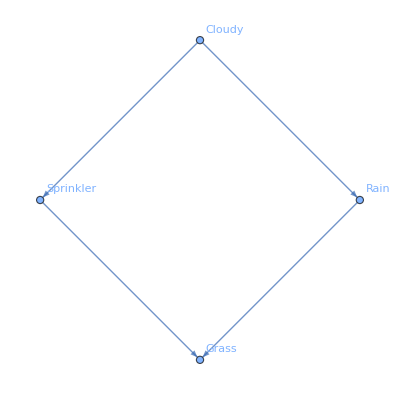

## Introduction

Bayesian Networks (BNs) are graphical probabilistic models for compact representation of categorical multivariate distributions . While the number of state combinations rapidly explodes with the number of variables, BN take advantage of the conditional dependencies to express distributions more efficiently in the factored form of a directed acyclic graph (DAG) .  For example, we could express P(X,Y,Z) as P(X)P(Y)P(Z|X,Y) if we know how Z depends on X and Y.
BNs are commonly for risk analysis and decision - support systems where one is interested in the effect of evidence on predictions . 
   
  If I were to implement a BN framework in any other language, a large part of the job would probably be to implement the inference algorithms . However, the WL already has a lot of high - level functionality for probabilistic analysis . In fact, one should in principle be able to just do something like Probability[x == "A" \[Conditioned] y == "B" && z == "C", {x, y, z} \[Distributed] dist]. Moreover, the WL has a CategoricalDistribution and support support for creating compound distributions using ProbabilityDistribution . However, there are two issues :

It appears that ProbabilityDistribution does not support categorical domains directly, so I had to find a workaround.

It is inconvenient to use constructs like {x, y, z} \[Distributed] dist because one has to remember the ordering of the variables.

### Solving issue 1: Making ProbabilityDistribution work with categorical variables

To solve the first issue, I noted that there are two ways to implement categorical distributions in the WL:

```mathematica
dist1 = CategoricalDistribution[{"A","B","C"},{0.1,0.2,0.7}]
```

CategoricalDistribution[…]

```mathematica
dist2 = EmpiricalDistribution[{0.1,0.2,0.7}->{"A","B","C"}]
```

DataDistribution[…]

However, note that EmpiricalDistribution produces a DataDistribution, and dist1 and dist2 behave differently when we try to retrieve their PDF functions:

```mathematica
PDF[dist1,x]
```

PDF[CategoricalDistribution[…],x]

```mathematica
PDF[dist2,x]
```

0.1 Boole[A==x]+0.2 Boole[B==x]+0.7 Boole[C==x]

EmpiricalDistribution directly produces a symbolic PDF function in terms of Boole . This is exactly what I need to be able to construct multivariate distributions in my BN model,  however, the domain is still categorical, which ProbabilityDistribution doesn’t like. To solve this, I introduce a domain mapping, e.g. <|”A”->1,”B”->2,”C”->3|>.

My implementation of BayesianNetwork accepts both CategoricalDistribution and EmpiricalDistribution as input, but represent all distributions internally as DataDistribution with integer range domains, e.g.:

```mathematica
dist3 = EmpiricalDistribution[{0.1,0.2,0.7}->{1,2,3}]
```

DataDistribution[…]

### Solving issue 2 : Making Probability work with named variables

The  Probability function in the WL works with multivariate distributions, however one has to specify the order of the variables, e.g., {x, y, z} \[Distributed] dist. 
To overcome this, my BayesianNetwork makes use of named variables using #name (Slot[“name”]).  I then overloaded the Probability function so that it works with constructs like Probability[#var2 \[Conditioned] #var1 && #var3 &, BN].

## Examples

Before going in detail about the implementation, let me show a small example, one that is commonly used to teach BNs:

```mathematica
BN = BayesianNetwork[{
<|"Name"->"Cloudy","Distribution"->Function[CategoricalDistribution[{"True","False"},{0.5,0.5}]]|>,
<|"Name"->"Rain","Distribution"->Function[CategoricalDistribution[{"True","False"},Boole[#Cloudy=="True"]{0.8,0.2}+Boole[#Cloudy=="False"]{0.2,0.8}]]|>,
<|"Name"->"Sprinkler","Distribution"->Function[CategoricalDistribution[{"On","Off"},Boole[#Cloudy=="True"]{0.1,0.9}+Boole[#Cloudy=="False"]{0.5,0.5}]]|>,
<|"Name"->"Grass","Distribution"->Function[CategoricalDistribution[{"Wet","Dry"},Boole[#Rain=="True"&&#Sprinkler=="On"]{0.99,0.01}+ Boole[#Rain=="False"&&#Sprinkler=="On"]{0.9,0.1}+Boole[#Rain=="True"&&#Sprinkler=="Off"]{0.9,0.1}+Boole[#Rain=="False"&&#Sprinkler=="Off"]{0.0,1.0}]]|>
}]
```

BayesianNetworkObject[…]

Note that each variable has a name and a distribution, and the distributions are wrapped inside Function[]. The named function variables are used to infer parent relationships between the variables.

We can now compute some probabilities:

```mathematica
Probability[#Cloudy =="True"\[Conditioned] #Rain =="True"&,BN]
```

0.8

```mathematica
Probability[#Sprinkler=="On"\[Conditioned] #Grass =="Wet"&,BN]
```

0.429764

We can also plot the BN, with and without some evidence:

```mathematica
Graph[BN]
```

-Graphics-

```mathematica
Graph[BN,#Rain=="True"&]
```

-Graphics-

Lets see what happens if we make one of the distributions symbolic:

```mathematica
BN = BayesianNetwork[{
<|"Name"->"Cloudy","Distribution"->Function[CategoricalDistribution[{"True","False"},{0.5,0.5}]]|>,
<|"Name"->"Rain","Distribution"->Function[CategoricalDistribution[{"True","False"},Boole[#Cloudy=="True"]{p,1-p}+Boole[#Cloudy=="False"]{q,1-q}]]|>,
<|"Name"->"Sprinkler","Distribution"->Function[CategoricalDistribution[{"On","Off"},Boole[#Cloudy=="True"]{0.1,0.9}+Boole[#Cloudy=="False"]{0.5,0.5}]]|>,
<|"Name"->"Grass","Distribution"->Function[CategoricalDistribution[{"Wet","Dry"},Boole[#Rain=="True"&&#Sprinkler=="On"]{0.99,0.01}+ Boole[#Rain=="False"&&#Sprinkler=="On"]{0.9,0.1}+Boole[#Rain=="True"&&#Sprinkler=="Off"]{0.9,0.1}+Boole[#Rain=="False"&&#Sprinkler=="Off"]{0.0,1.0}]]|>
}]
```

BayesianNetworkObject[…]

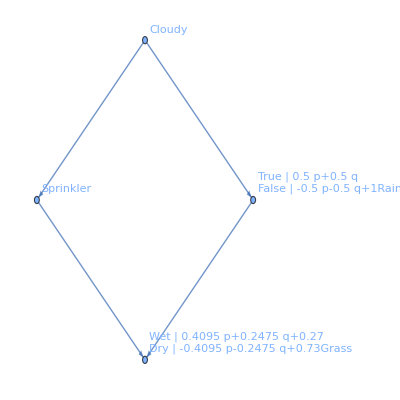

```mathematica
Graph[BN]
```

We can even make everything symbolic:

```mathematica
BN = BayesianNetwork[{
<|"Name"->"Cloudy","Distribution"->Function[CategoricalDistribution[{"True","False"},{pC,1-pC}]]|>,
<|"Name"->"Rain","Distribution"->Function[CategoricalDistribution[{"True","False"},Boole[#Cloudy=="True"]{pRc,1-pRc}+Boole[#Cloudy=="False"]{pRnc,1-pRnc}]]|>,
<|"Name"->"Sprinkler","Distribution"->Function[CategoricalDistribution[{"On","Off"},Boole[#Cloudy=="True"]{pSc,1-pSc}+Boole[#Cloudy=="False"]{pSnc,1-pSnc}]]|>,
<|"Name"->"Grass","Distribution"->Function[CategoricalDistribution[{"Wet","Dry"},Boole[#Rain=="True"&&#Sprinkler=="On"]{pGrs,1-pGrs}+ Boole[#Rain=="False"&&#Sprinkler=="On"]{pGnrs,1-pGnrs}+Boole[#Rain=="True"&&#Sprinkler=="Off"]{pGrns,1-pGrns}+Boole[#Rain=="False"&&#Sprinkler=="Off"]{pGnrns,1-pGnrns}]]|>
}];

Probability[#Cloudy== c\[Conditioned]#Grass=="Wet"&,BN]
```

(pC (pGnrns (-1+pRc) (-1+pSc)+(pGnrs-pGnrs pRc+pGrs pRc) pSc+pGrns (pRc-pRc pSc)) Boole[c==1]-(-1+pC) (pGnrns (-1+pRnc) (-1+pSnc)+(pGnrs-pGnrs pRnc+pGrs pRnc) pSnc+pGrns (pRnc-pRnc pSnc)) Boole[c==2])/(pGrns pRnc+pC pGrns (pRc-pRc pSc+pRnc (-1+pSnc))+pGnrns (-1+pRnc) (-1+pSnc)+pGnrs pSnc-pGnrs pRnc pSnc-pGrns pRnc pSnc+pGrs pRnc pSnc+pC pGnrs (pSc-pRc pSc+(-1+pRnc) pSnc)+pC pGrs (pRc pSc-pRnc pSnc)+pC pGnrns (pRnc+pRc (-1+pSc)-pSc+pSnc-pRnc pSnc))

We can also ask more complicated queries:

```mathematica
Probability[#Grass =="Wet"∧#Cloudy=="False"\[Conditioned] #Rain =="True"∨#Sprinkler == "On"&,BN]
```

((-1+pC) (pGrns pRnc (-1+pSnc)+pGnrs (-1+pRnc) pSnc-pGrs pRnc pSnc))/(pRnc+pC (pRc+pSc-pRc pSc+pRnc (-1+pSnc)-pSnc)+pSnc-pRnc pSnc)

```mathematica
Probability[#Grass =="Wet"⊽#Cloudy=="False"⊻#Sprinkler=="On"\[Conditioned] #Rain =="True"&,BN]
```

(pC (-1+pGrns) pRc (-1+pSc)-(-1+pGrs) pRnc pSnc+pC (-1+pGrs) pRnc pSnc)/(pC (pRc-pRnc)+pRnc)

## How it works

The following code implements a BayesianNetwork function that produces a BayesiannetworkObject:

```mathematica
(* Creating Bayesian network models *)
BayesianNetwork[vars_?(VectorQ[#,AssociationQ]&)] := Module[{names,name2slot,x,a,distributions,parents,edges,graph,args,originalDomains,newDomains,domainmaps,transformationrules,pdf,ranges,dist},
	names = vars[[All,"Name"]];
	distributions = vars[[All,"Distribution"]];
	name2slot = Association@@Table[names[[i]]->Slot[i],{i,Length@names}];
	
	(* Create BN graph*)
	parents = Table[DeleteDuplicates[Cases[dist,Slot[a_]->a,-1]],{dist,distributions}]; (* Extracts all variable slots in the distribution expressions *)
	edges = Flatten[Table[Table[parents[[i,j]]->names[[i]],{j,Length@parents[[i]]}],{i,Length@names}]];
	graph = Graph[edges,VertexLabels->Automatic];
	
	(* Transform all distributions to integer domains *)
	originalDomains = Map[DistributionDomain[#[[1]]]&,distributions];
	newDomains = Map[Range@Length@#&,originalDomains];	
	domainmaps = MapThread[Association@@Thread[#1->#2]&,{originalDomains,newDomains}];
	transformationrules = Flatten@Table[
		Module[{slot,dom},
			dom = domainmaps[[i]];
			slot = Slot@names[[i]];
			MapThread[Equal[slot,#1]->Equal[slot,#2]&,{Keys[dom],Values[dom]}]
		],
	{i,Length@distributions}];
	distributions = distributions/.transformationrules;
	
	(* Replace named variables by dummy variables*)		
	args = Map[Thread[name2slot[[#]]]&,parents];
	distributions = MapThread[#1[#2]&,{distributions,args}];
	distributions = Table[
		Module[{dom,probs},
			dom = DistributionDomain[dist];
			probs = Table[Evaluate[PDF[dist,y]],{y,dom}];
			EmpiricalDistribution[probs->Range@Length@dom]
		]
	,{dist,distributions}];

	(* Create joint distribution *)
	pdf = Function[Evaluate[Times@@Table[PDF[distributions[[i]],Slot[i]],{i,Length@distributions}]]];
	ranges = Table[{x[i],Sequence@@MinMax[DistributionDomain[distributions[[i]]]],1},{i,Length@distributions}];
	dist = ProbabilityDistribution[pdf@@Table[x[i],{i,Length@distributions}],Sequence@@ranges];

	(* Return BM object *)
	BayesianNetworkObject[<|"Variables"->Table[<|"Name"->names[[i]],"Parents"->parents[[i]],"Domain"->domainmaps[[i]],"Distribution"->distributions[[i]]|>,{i,Length@names}],"Distribution"->dist,"Graph"->graph|>]
]
```

As an attempt to make my BN feel more WL native, the following additional code make the BayesianNetworkObject appear in the “iconized” form:

```mathematica
(* Visual appearance of BN objects *)
BayesianNetworkObject/:MakeBoxes[obj:BayesianNetworkObject[asc_?BayesianNetworkQ],form:(StandardForm|TraditionalForm)]:=
Module[{info},
	info={{BoxForm`SummaryItem[{Graph[asc["Graph"],VertexLabels->None,VertexSize->Large,ImageSize->50]}]}};
	BoxForm`ArrangeSummaryBox[BayesianNetworkObject,obj,None,info,{},form,"Interpretable"->Automatic]
]

(* Initialization tests *)
BayesianNetworkQ[asc_?AssociationQ] := AllTrue[{"Variables","Distribution","Graph"}, KeyExistsQ[asc, #]&]
```

The I overload the Probability function:

```mathematica
(* Calculation of probabilities *)
Unprotect[Probability];
BayesianNetworkObject/: Probability[expr_Function,BN_BayesianNetworkObject]:= Module[{variables,variableNames,variableSlots,variableAssociation,dom,dist,x,rules,newexpr,slot},
	variables = BN[[1,"Variables"]];
	variableNames = variables[[All,"Name"]];
	variableSlots = Table[x[i],{i,Length@variableNames}];
	variableAssociation = Association[Thread[variableNames->variableSlots]];

	(* Transform expression to the BN dummy variables with integer domains *)
	newexpr = expr; 
	Do[
		dom = variables[[i]]["Domain"];
		slot = Slot@variableNames[[i]];
		rules = MapThread[Equal[slot,#1]->Equal[slot,#2]&,{Keys[dom],Values[dom]}];
		newexpr = (newexpr/.rules),
	{i,Length@variables}];

	(* Compute the probability *)
	Probability[newexpr[variableAssociation],variableSlots \[Distributed] BN[[1,"Distribution"]]]/.{0.->0,1.->1}

]
Protect[Probability];
```

Finally, I overloaded the Graph function to create plots of the Bayesian networks:

```mathematica
(* Plotting *)
Unprotect[Graph];
BayesianNetworkObject/: Graph[BN_BayesianNetworkObject,evidence_:None,OptionsPattern[]]:= Module[{options,variables,graph,evidencenodes,a,colour,labels,probs,domain,outcomes,barcharts},
	options = Options[Graph];
	variables = BN[[1,"Variables"]];
	graph = BN[[1,"Graph"]];
	
	If[evidence===None,
		evidencenodes = {},
		evidencenodes = DeleteDuplicates[Cases[evidence,Slot[a_]->a,-1]]
	];

	labels = Table[
		domain = {Slot[var["Name"]],Sequence@@MinMax[var["Domain"]],1};
		If[evidence===None,
			probs = Simplify[Table[Probability[Evaluate[Slot[var["Name"]]==val]&,BN],{val,Keys[var["Domain"]]}]/.{0.->0,1.->1}],
			probs = Simplify[Table[Probability[Evaluate[Slot[var["Name"]]==val\[Conditioned] evidence[[1]]]&,BN],{val,Keys[var["Domain"]]}]/.{0.->0,1.->1}]
		];
		If[VectorQ[probs,NumericQ],
			var["Name"]->Labeled[
				BarChart[probs,PlotRange->{0,1},BarOrigin->Left,ImageSize->Tiny,Frame->True,FrameTicks->{None,Automatic},ChartLabels->Keys[var["Domain"]],ChartStyle->If[MemberQ[evidencenodes,var["Name"]],Blue,Orange]],
				var["Name"],Top],
			var["Name"]->Labeled[TableForm[probs,TableHeadings->{Keys[var["Domain"]],None}],var["Name"],Top]
		],{var,variables}];
	
	Graph[graph,VertexLabels->labels]
]
Protect[Graph];
```

That’s all the code I needed to implement BNs in the WL!

## Concluding remarks

I’m quite happy that I was able to implement BNs in WL with such a small amount of code. Also, this implementation is the only one I know of that works with symbolic probabilities, which is sometimes convenient when I’m not confident enough to assign a number. With this implementation I can still perform inference and investigate how the answer varies as I change parameters. Also, the types of queries I can ask are more advanced than what I have seen in other implementations. 

Of course there are also limitations.  Most notably, the probability calculations becomes very slow as soon as one goes beyond small “toy examples” like I presented here. However, this is not surprising given that I haven’t implemented any efficient BN inference algorithms and solely rely on the inbuilt Probability function to do the calculations. One could possibly write new methods for Probability to mitigate this. 

I hope the Wolfram will include support for BNs in the future so that my paclet becomes redundant, for example as an update to CategoricalDistribution. In the meantime, I would be interested to hear from others who have tried to implement BNs in the WL.